# Supplementary tensors

## ITensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.037917,Null}

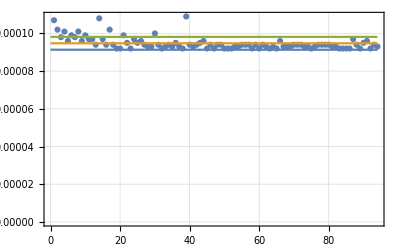

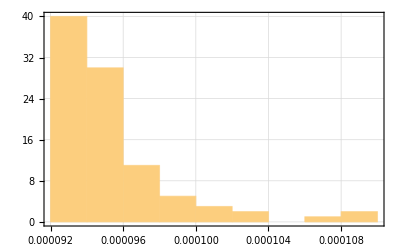

{0.0000913568,0.000094766,0.0000981751}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[2]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.068423,Null}

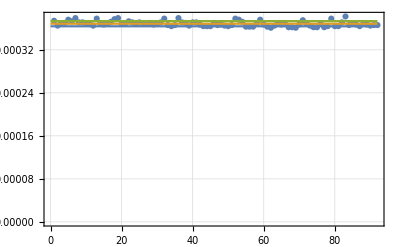

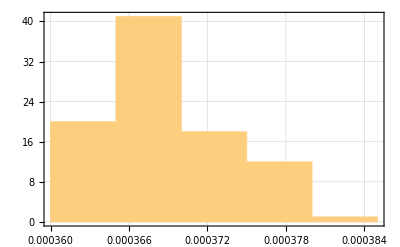

{0.000363719,0.000368522,0.000373324}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[3]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.441249,Null}

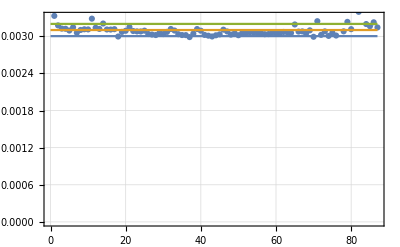

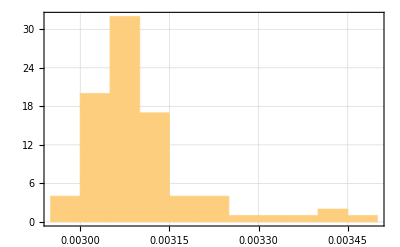

{0.00300338,0.00310216,0.00320095}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[4]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{4.51257,Null}

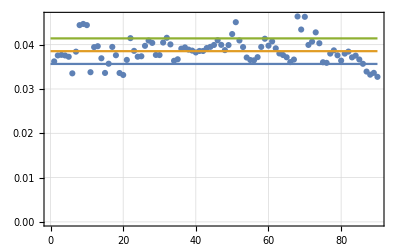

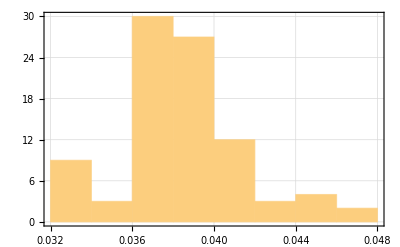

{0.0356539,0.0385377,0.0414214}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[5]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{162.465,Null}

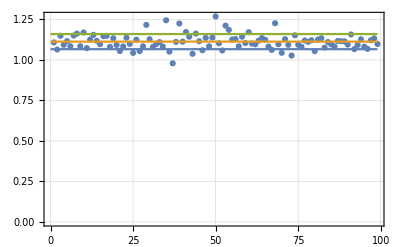

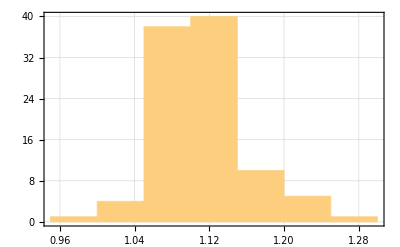

{1.06604,1.11276,1.15949}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[6]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.087237,Null}

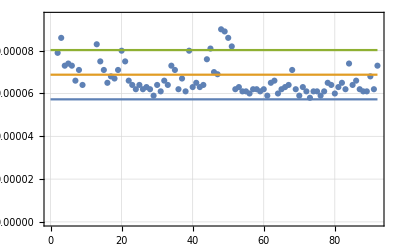

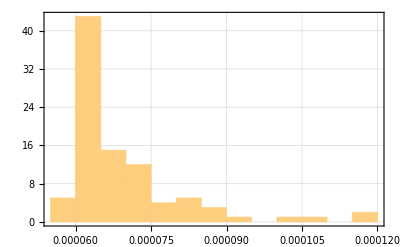

{0.0000572698,0.0000687826,0.0000802955}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.088908,Null}

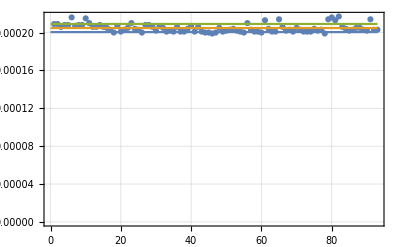

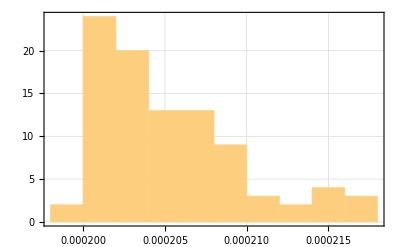

{0.000200485,0.000204774,0.000209063}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.4051,Null}

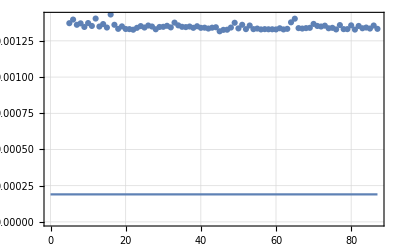

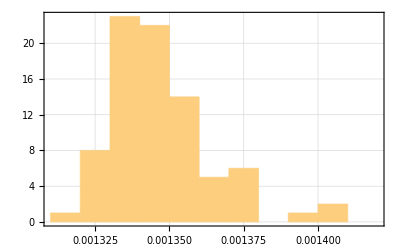

{0.000190016,0.00167033,0.00315065}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.56705,Null}

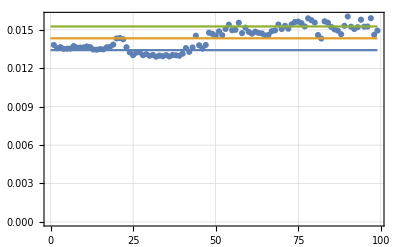

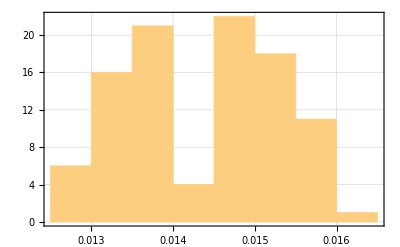

{0.0134182,0.0143432,0.0152681}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{20.925,Null}

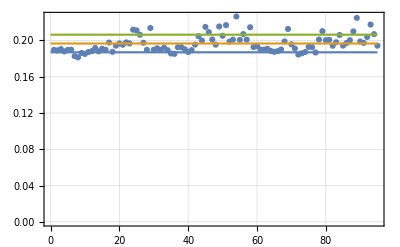

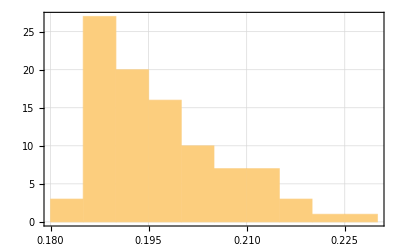

{0.186945,0.196655,0.206365}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{324.545,Null}

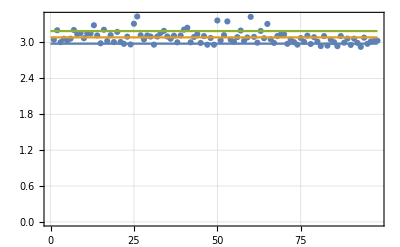

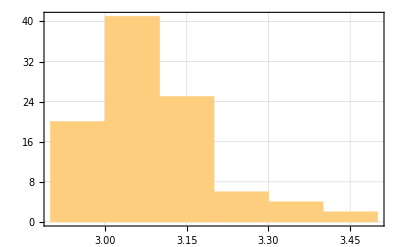

{2.97988,3.08546,3.19105}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C1Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.082963,Null}

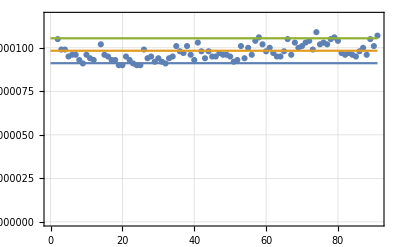

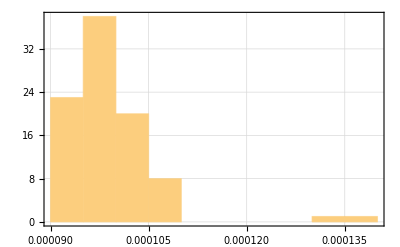

{0.0000911543,0.0000983077,0.000105461}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.108845,Null}

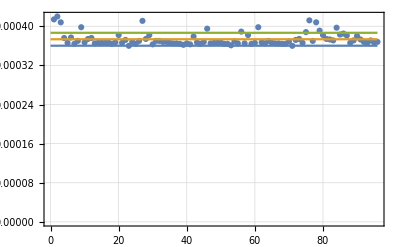

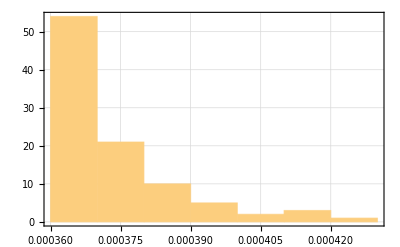

{0.000360185,0.000373385,0.000386585}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.33533,Null}

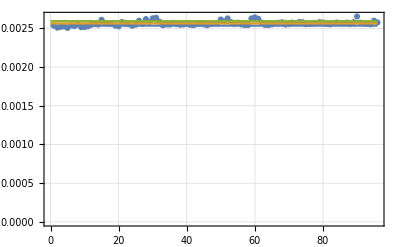

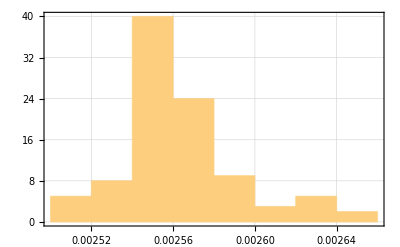

{0.00253419,0.00256322,0.00259225}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.94766,Null}

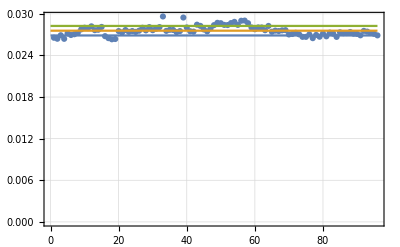

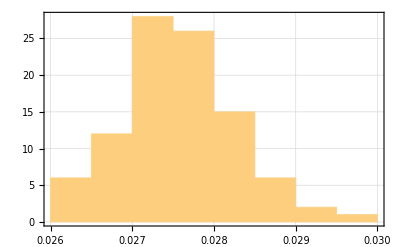

{0.0268784,0.0275651,0.0282518}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{37.0456,Null}

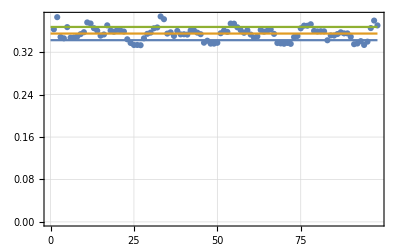

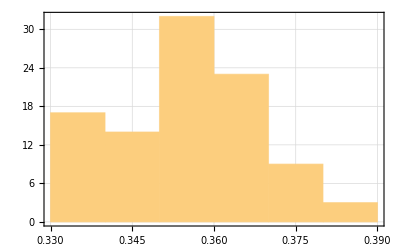

{0.342705,0.355177,0.367648}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{592.676,Null}

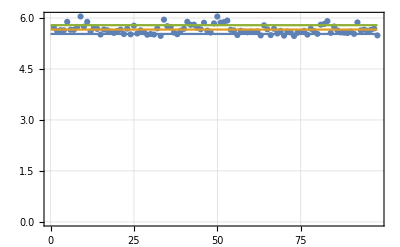

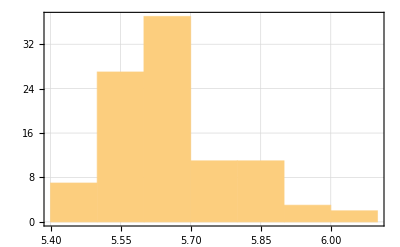

{5.53021,5.65941,5.78862}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C2Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.150845,Null}

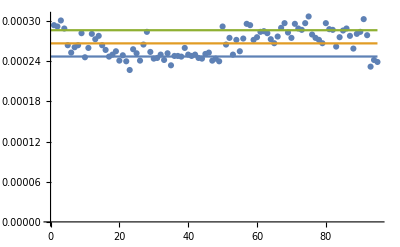

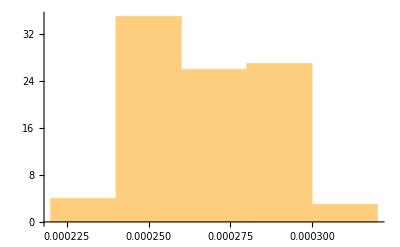

{0.00024713,0.000266779,0.000286428}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.138857,Null}

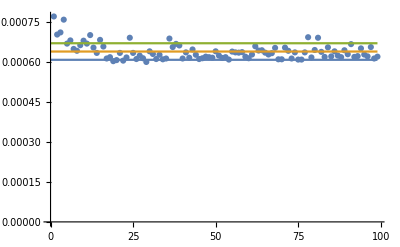

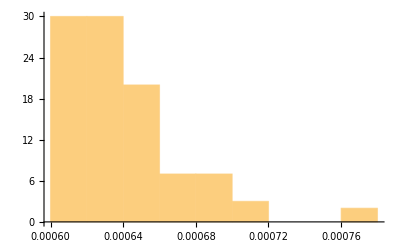

{0.000609074,0.000640202,0.00067133}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.570881,Null}

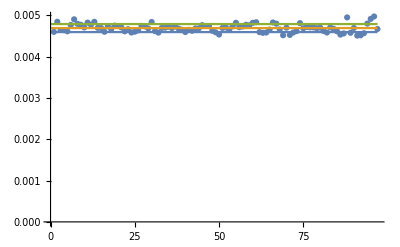

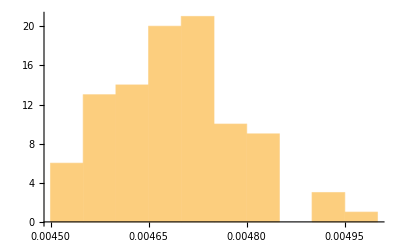

{0.00459376,0.00469093,0.00478809}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{5.1724,Null}

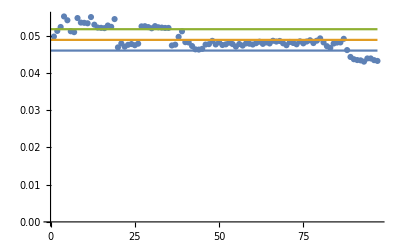

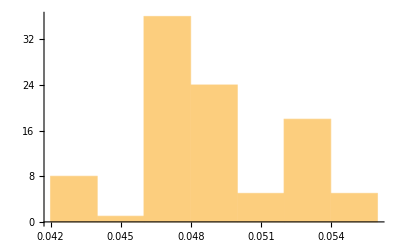

{0.045997,0.0488659,0.0517348}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{66.4878,Null}

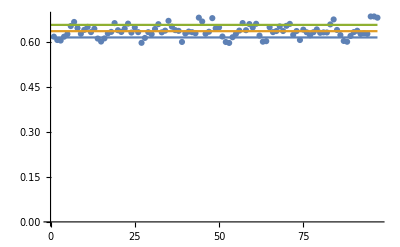

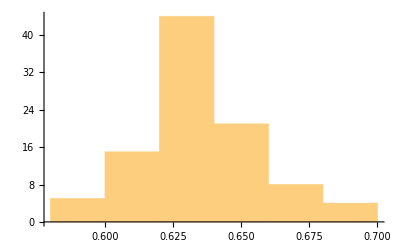

{0.614223,0.635128,0.656033}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1065.58,Null}

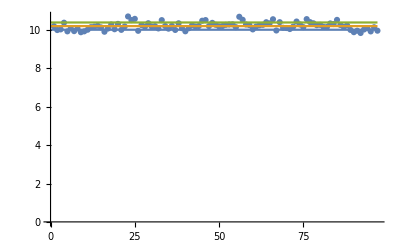

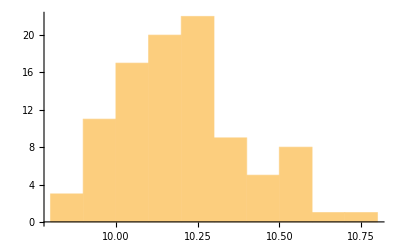

{10.0137,10.2026,10.3915}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C3Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.094955,Null}

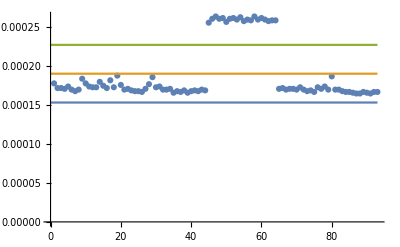

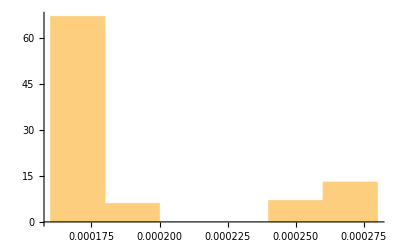

{0.000153396,0.000190441,0.000227485}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.159534,Null}

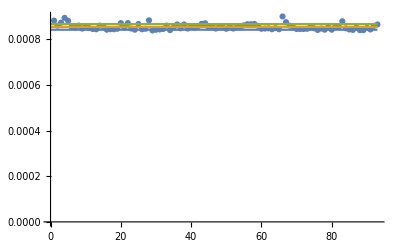

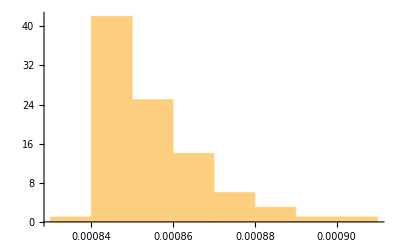

{0.000841875,0.000854226,0.000866577}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.76422,Null}

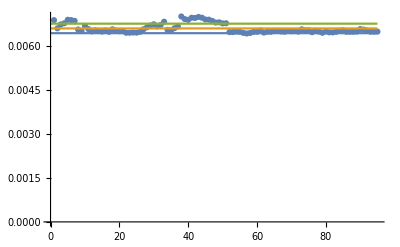

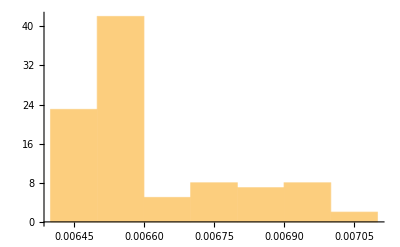

{0.0064515,0.00661414,0.00677677}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{7.228,Null}

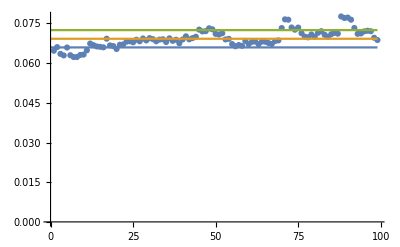

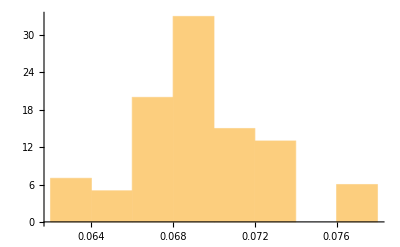

{0.0659356,0.0692038,0.0724719}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{94.11,Null}

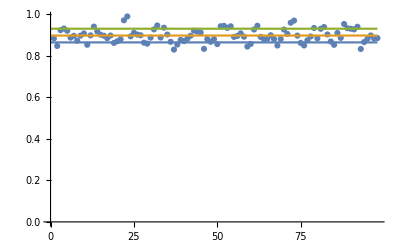

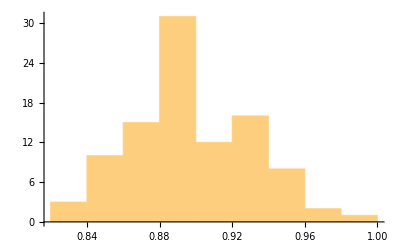

{0.864089,0.897033,0.929977}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1579.33,Null}

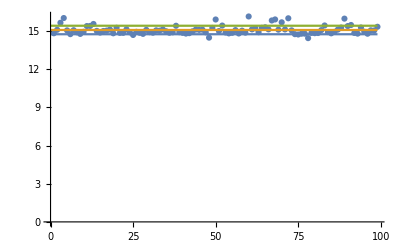

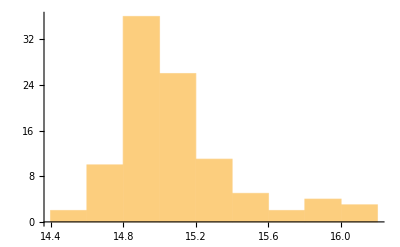

{14.7477,15.0819,15.4161}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C4Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.102365,Null}

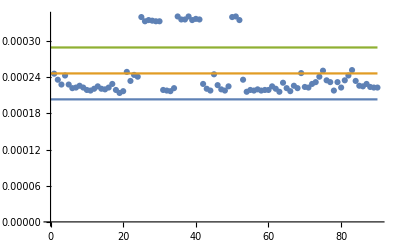

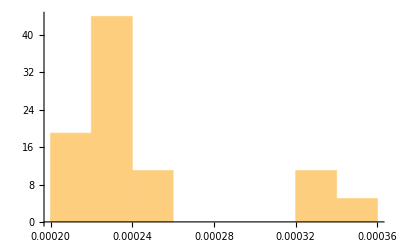

{0.00020338,0.000246444,0.000289509}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.204927,Null}

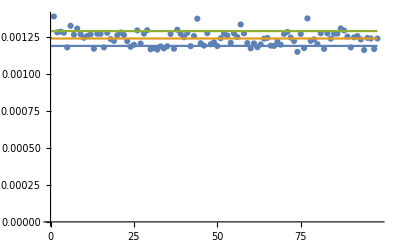

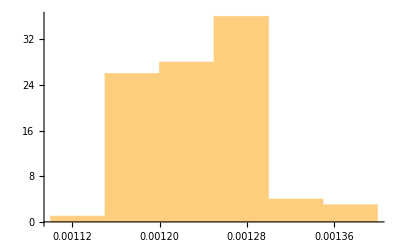

{0.00118901,0.00123905,0.00128909}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.0987,Null}

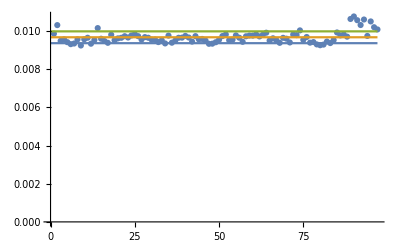

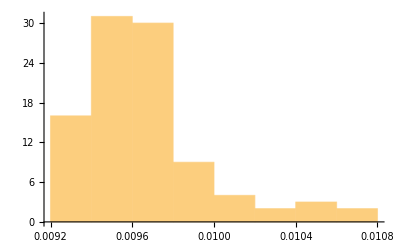

{0.00935873,0.00966827,0.00997781}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{10.5664,Null}

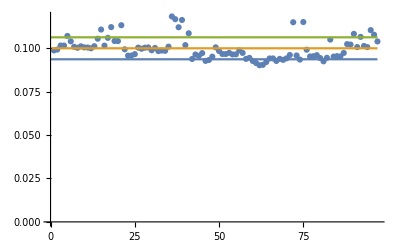

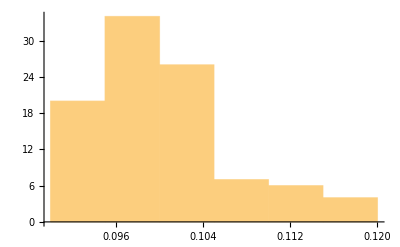

{0.0936306,0.0999565,0.106283}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{131.925,Null}

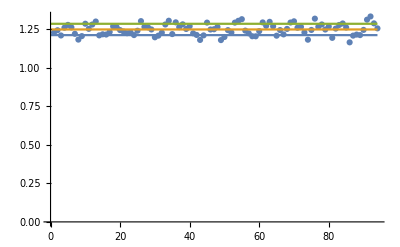

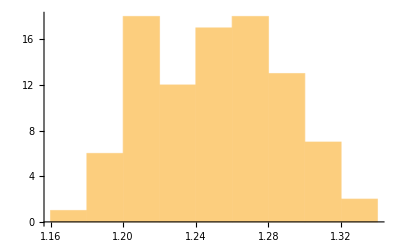

{1.21316,1.24995,1.28674}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.210531,Null}

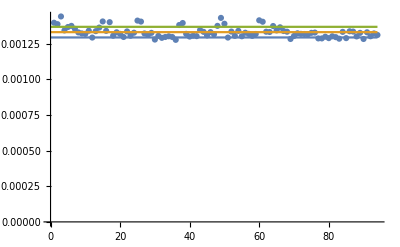

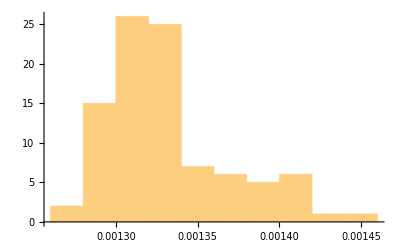

{0.00129371,0.00133096,0.0013682}

```mathematica
theData1 = {};
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{0.357652,Null}

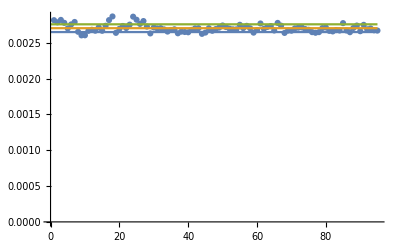

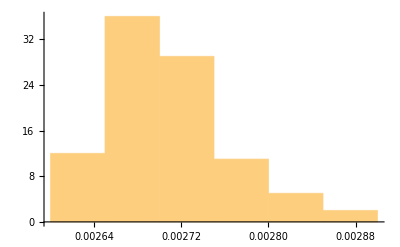

{0.00265104,0.00270518,0.00275932}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{0.543922,Null}

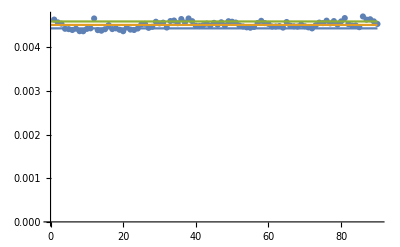

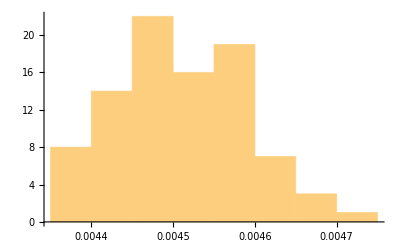

{0.00443133,0.00451036,0.00458938}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{0.746075,Null}

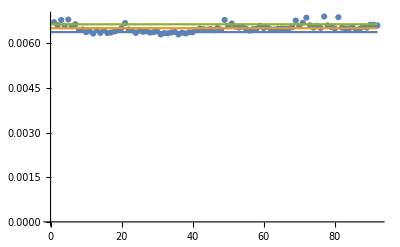

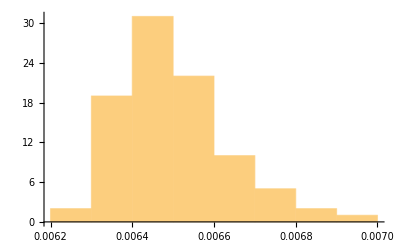

{0.00637449,0.00650574,0.00663699}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{1.10163,Null}

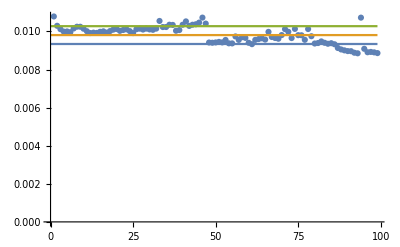

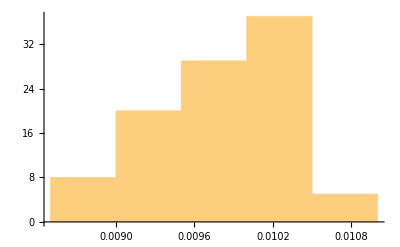

{0.00933952,0.00980725,0.010275}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{1.31916,Null}

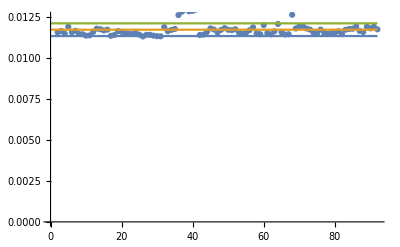

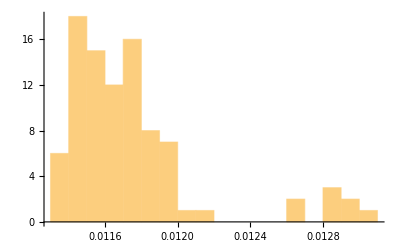

{0.0113602,0.0117485,0.0121368}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

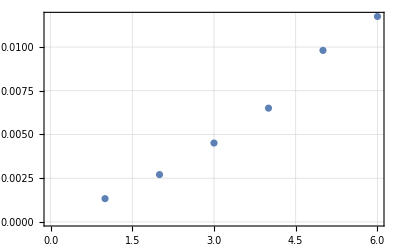

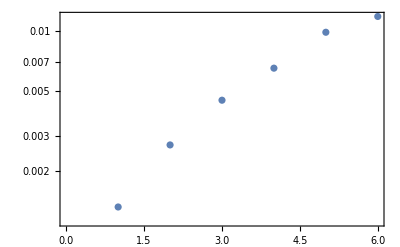

```mathematica
ListPlot[theData1,PlotTheme->"Detailed"]
ListLogPlot[theData1,PlotTheme->"Detailed"]
```

```mathematica
NotebookSave[]
```

# Scalar-graviton vertices

## Kinetic term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.584639,Null}

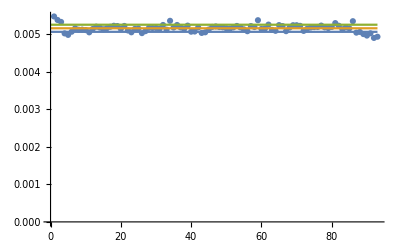

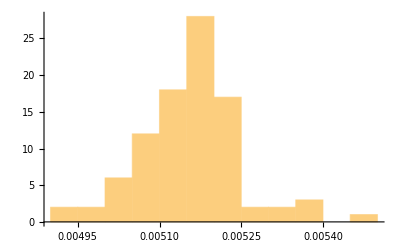

{0.00506421,0.00515898,0.00525375}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.0568,Null}

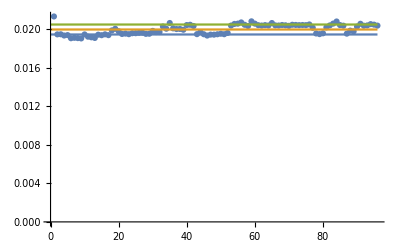

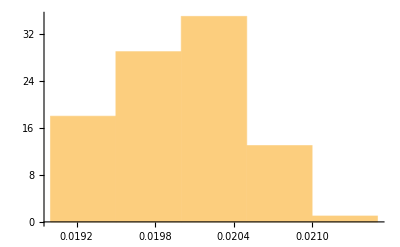

{0.0194816,0.0199989,0.0205163}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{37.8309,Null}

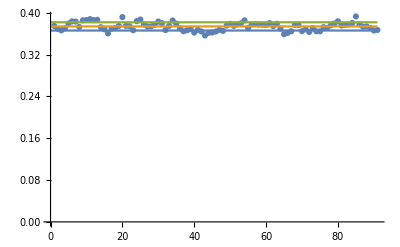

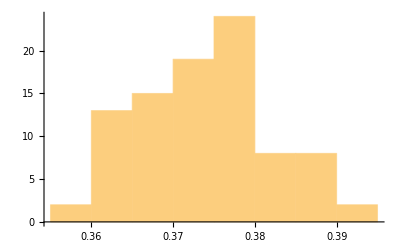

{0.366077,0.373958,0.381839}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Potential term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.049902,Null}

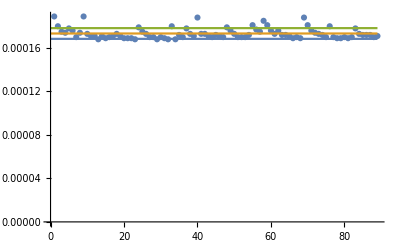

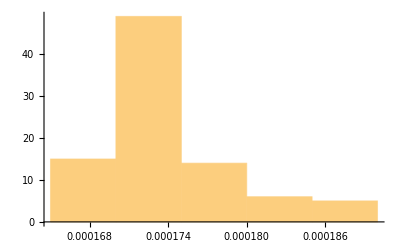

{0.000168388,0.000173326,0.000178264}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[1],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.067227,Null}

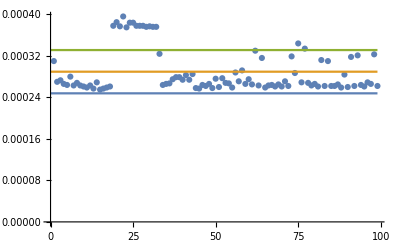

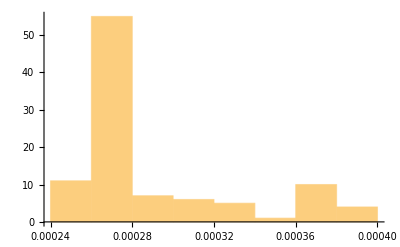

{0.000247816,0.000289525,0.000331234}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[2],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.102959,Null}

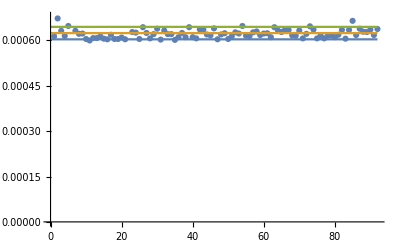

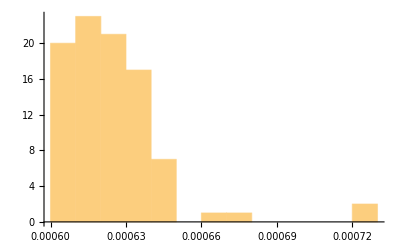

{0.000603838,0.000624467,0.000645097}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[3],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-fermion vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.535343,Null}

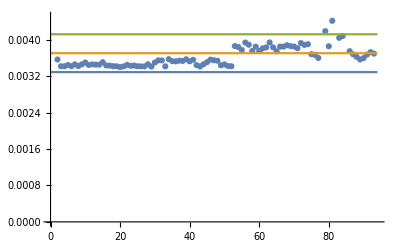

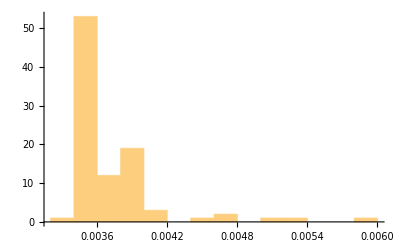

{0.00328597,0.0037013,0.00411663}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.09279,Null}

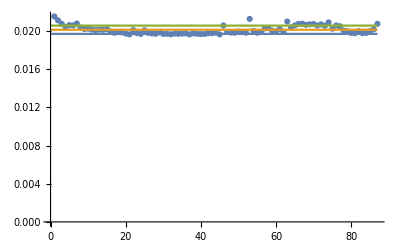

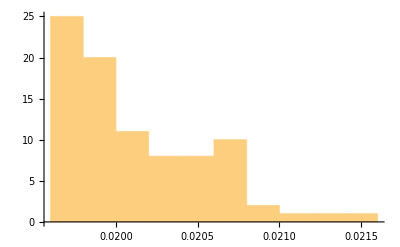

{0.0196973,0.0201302,0.020563}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{21.271,Null}

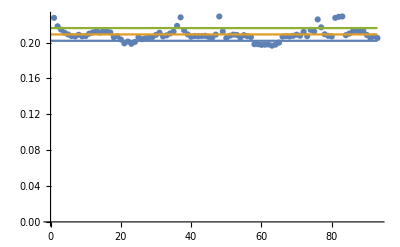

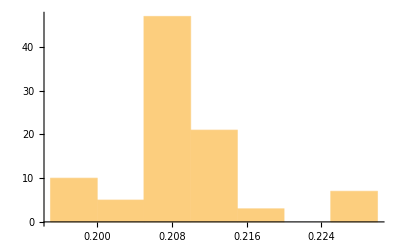

{0.202011,0.209103,0.216194}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-vector vertices

## Massive vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{2.69415,Null}

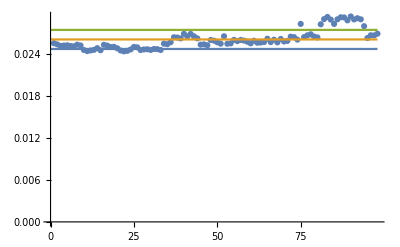

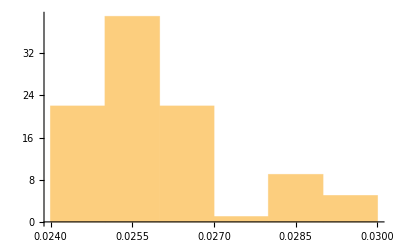

{0.0246659,0.026025,0.0273842}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[1],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{25.1066,Null}

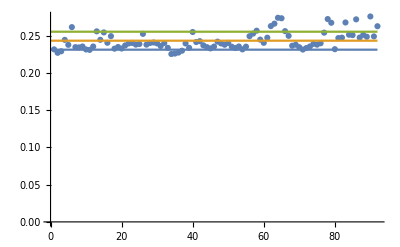

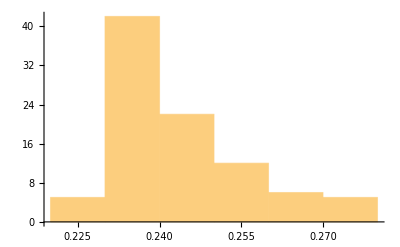

{0.231465,0.24354,0.255615}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[2],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{335.327,Null}

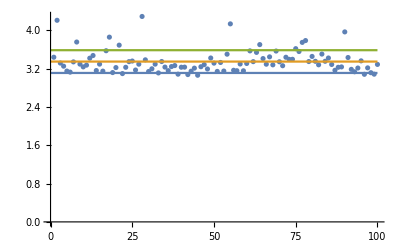

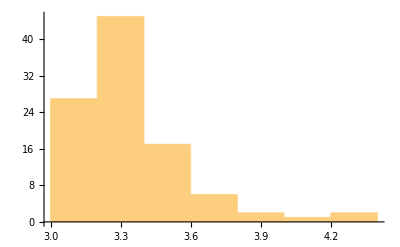

{3.11245,3.3504,3.58834}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[3],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Massless vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{4.546,Null}

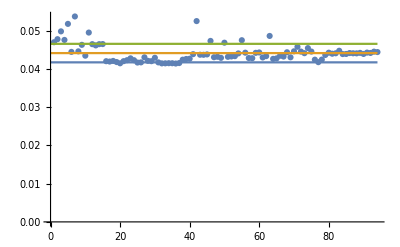

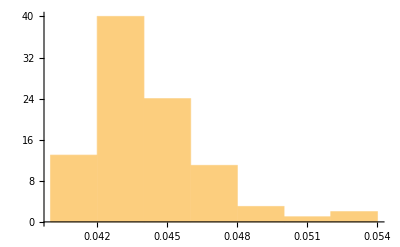

{0.0417258,0.0441453,0.0465648}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[1],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{62.441,Null}

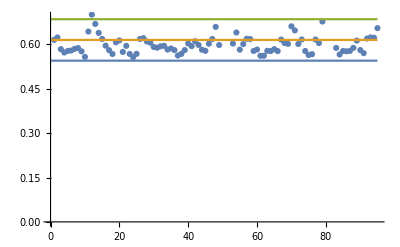

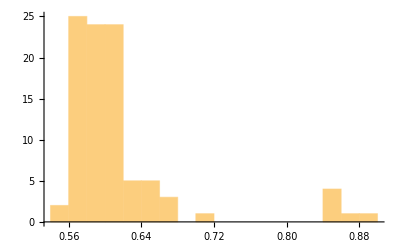

{0.545026,0.615131,0.685237}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[2],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[3],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Ghosts

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.362873,Null}

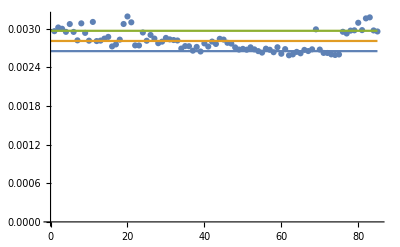

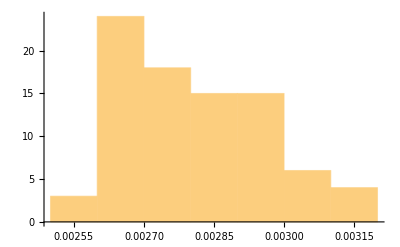

{0.00265066,0.00280848,0.00296631}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[1],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.88871,Null}

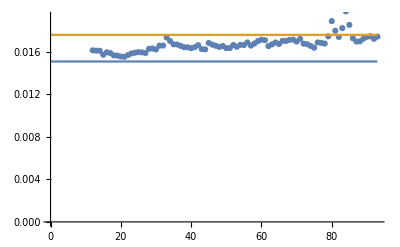

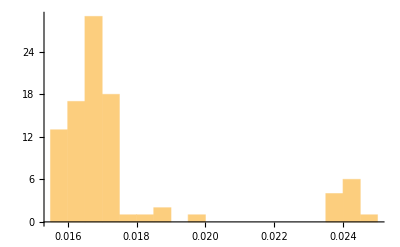

{0.0150827,0.0175866,0.0200905}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[2],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{17.4075,Null}

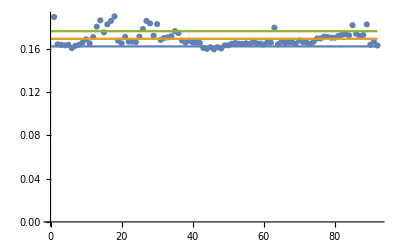

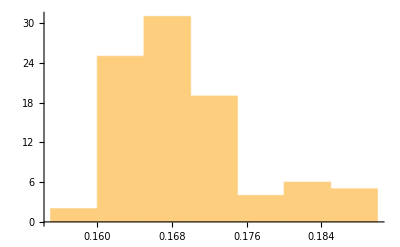

{0.162189,0.16921,0.176231}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[3],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton vertices

## Pure graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{14.9892,Null}

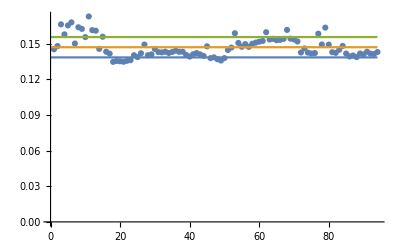

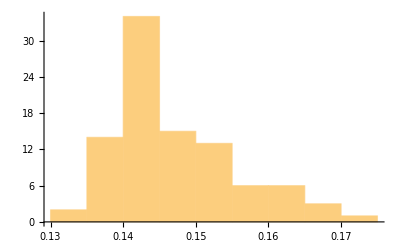

{0.138511,0.14708,0.155649}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[2],ε]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{673.137,Null}

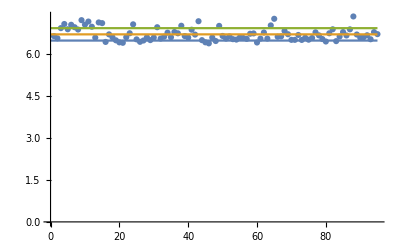

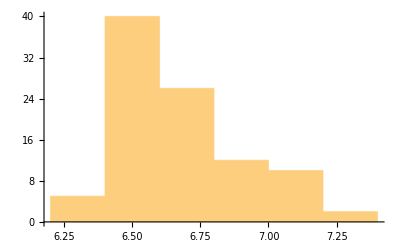

{6.46179,6.6829,6.904}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[3],ε]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Graviton-ghost vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{4.83899,Null}

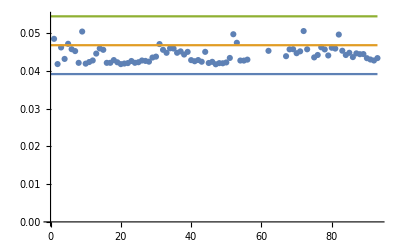

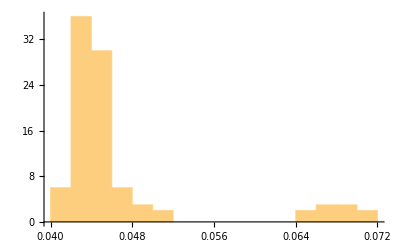

{0.0391109,0.0467495,0.0543881}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[1],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{99.2485,Null}

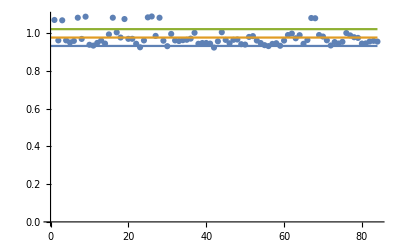

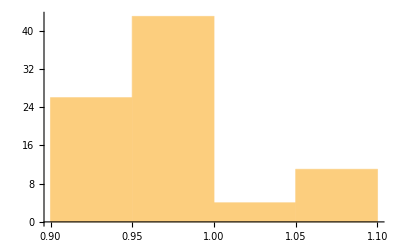

{0.932293,0.976816,1.02134}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[2],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1887.93,Null}

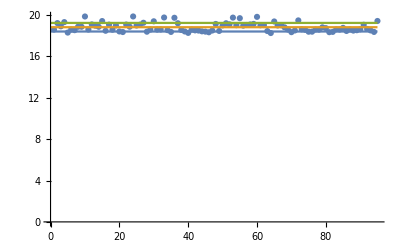

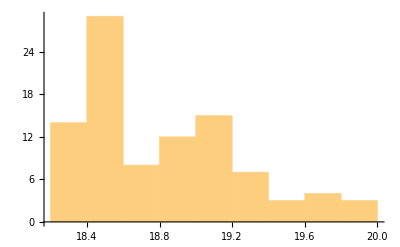

{18.4073,18.8225,19.2378}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[3],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```